```mathematica
1.Naloga
(x^5-2 x^2+3x+4)/(x^5-2x-1) /.  x-> {1,2,3,4}
```

{-3,34/27,119/118,144/145}

```mathematica
racun :=(x^5-2 x^2+3x+4)/(x^5-2x-1)
racun /. x-> {1,2,3,4}
```

{-3,34/27,119/118,144/145}

```mathematica
tabela =Table[x,{x,10}]
racun /. x-> tabela
```

{1,2,3,4,5,6,7,8,9,10}

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
2.Naloga
sez = Table[x*10,{x,7}]
```

{10,20,30,40,50,60,70}

```mathematica
sez[[{1,2,3}]]
```

{10,20,30}

```mathematica
Take[sez,-2]
```

{60,70}

```mathematica
sez[[{2,3,4}]]
```

{20,30,40}

```mathematica
sez[[{2,3,5}]]
```

{20,30,50}

```mathematica
sez[[{1,2,3,6,7}]]
```

{10,20,30,60,70}

```mathematica
3.Naloga
sez2 ={x^6,x^2,a}
sez2 /. x -> 3
```

{x^6,x^2,a}

{729,9,a}

```mathematica
sez2 /. x -> x^2
```

{x^12,x^4,a}

```mathematica
sez2 /. x^2-> x
```

{x^6,x,a}

```mathematica
sez2 /. x -> {1,2,3}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez2 /. {{x-> 3},{a -> z} }
```

{{729,9,a},{x^6,x^2,z}}

```mathematica
ReplaceRepeated[sez2 /. {{x-> 3},{a -> z} }]
```

ReplaceRepeated[{{729,9,a},{x^6,x^2,z}}]

```mathematica
4.Naloga
```

```mathematica
D[x^5+4 x^3-9,x]
```

12 x^2+5 x^4

```mathematica
D[x^5+4 x^3-9,x] /. x -> {1,5}
```

{17,3425}

```mathematica
D[ⅇ^(x^(1/4))]
```

ⅇ^(x^(1/4))

```mathematica
D[ⅇ^(x^(1/4))] /. x-> {1,2}
```

{ⅇ,ⅇ^(2^(1/4))}

General::ivar: x∈ is not a valid variable.

∂_(x∈ℝ) Abs'[1+x]

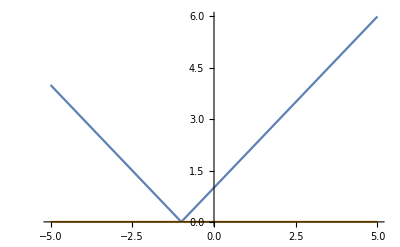

```mathematica
neki =FullSimplify[D[Abs[x+1],x,x ∈ Reals]]
Plot[{Abs[x+1],neki},{x,-5,5}]
```

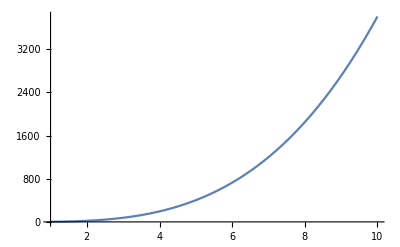

```mathematica
5.Naloga
f[x_] := x^3 Log[4x+5]
Plot[f[x],{x,1,10}]
```

```mathematica
x0 =5
k0=D[f[x],x] /. x-> x0
Solve[f[x0]==k0*x0+n,n]
n0 = n/. First[Solve[f[x0]==k0*x0+n,n]]
```

5

20+75 Log[25]

{{n→-50 (2+5 Log[25])}}

-50 (2+5 Log[25])